```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["VariationalMethods`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[Sd,γm,γp,q2SolDEL,h,k,m,r,q01,q02,v01,v02,q11,q12,qrecursive,σRK,EL]
```

```mathematica
(*k=0;*)
```

### Definition of the continuous Lagrangian and Rayleigh potential

```mathematica
n=2;
```

```mathematica
Q[t_]:={Q1[t],Q2[t]};
```

```mathematica
q0={q01,q02};
q1={q11,q12};
```

```mathematica
v0={v01,v02};
```

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]==ConstantArray[0,n]
```

```mathematica
L[q_,v_]:=1/2*v.v
```

```mathematica
R[q_,v_]=1/3*r*Sum[v[[i]]^3,{i,n}]
```

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

1/3 r (v⟦1⟧^3+v⟦2⟧^3)

```mathematica
f[q_,v_]=Table[-D[R[q,v],v[[i]]],{i,n}]
```

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::partd: Part specification v⟦2⟧ is longer than depth of object.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-r v⟦1⟧^2,-r v⟦2⟧^2}

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
Ld[q0_,q1_]:=h*L[(q0+q1)/2,(q1-q0)/h]
```

```mathematica
Rd[q0_,q1_]:=h^2/2*R[(q0+q1)/2,(q1-q0)/h]
```

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
Ldp[q0_,q1_]:=Ld[q0,q1]+Rd[q0,q1]
```

```mathematica
Ldm[q0_,q1_]:=Ld[q0,q1]-Rd[q0,q1]
```

```mathematica
fdp[q0_,q1_]:=h/2*f[(q0+q1)/2,(q1-q0)/h]
```

```mathematica
fdm[q0_,q1_]:=h/2*f[(q0+q1)/2,(q1-q0)/h];
```

```mathematica
fdp[{q01,q02},{q11,q12}]==-Grad[Rd[{q01,q02},{q11,q12}],{q11,q12}]&&fdm[{q01,q02},{q11,q12}]==Grad[Rd[{q01,q02},{q11,q12}],{q01,q02}]//Simplify
```

True

### Discrete Euler-Lagrange equations

```mathematica
Grad[Ldm[{q01,q02},{q11,q12}],{q11,q12}]+Grad[Ldp[{q11,q12},{q21,q22}],{q11,q12}]
```

{(-q01+q11)/h-(-q11+q21)/h-((-q01+q11)^2 r)/(2 h)-((-q11+q21)^2 r)/(2 h),(-q02+q12)/h-(-q12+q22)/h-((-q02+q12)^2 r)/(2 h)-((-q12+q22)^2 r)/(2 h)}

```mathematica
DEL:=Grad[Ldm[{q01,q02},{q11,q12}],{q11,q12}]+Grad[Ldp[{q11,q12},{q21,q22}],{q11,q12}]==0
```

```mathematica
solsDEL=Solve[DEL,{q21,q22}]
```

{{q21→(-1+q11 r-√(1-2 q01 r+2 q11 r-q01^2 r^2+2 q01 q11 r^2-q11^2 r^2))/r,q22→(-1+q12 r-√(1-2 q02 r+2 q12 r-q02^2 r^2+2 q02 q12 r^2-q12^2 r^2))/r},{q21→(-1+q11 r-√(1-2 q01 r+2 q11 r-q01^2 r^2+2 q01 q11 r^2-q11^2 r^2))/r,q22→(-1+q12 r+√(1-2 q02 r+2 q12 r-q02^2 r^2+2 q02 q12 r^2-q12^2 r^2))/r},{q21→(-1+q11 r+√(1-2 q01 r+2 q11 r-q01^2 r^2+2 q01 q11 r^2-q11^2 r^2))/r,q22→(-1+q12 r-√(1-2 q02 r+2 q12 r-q02^2 r^2+2 q02 q12 r^2-q12^2 r^2))/r},{q21→(-1+q11 r+√(1-2 q01 r+2 q11 r-q01^2 r^2+2 q01 q11 r^2-q11^2 r^2))/r,q22→(-1+q12 r+√(1-2 q02 r+2 q12 r-q02^2 r^2+2 q02 q12 r^2-q12^2 r^2))/r}}

```mathematica
solsDEL1={solsDEL[[4,1,2]],solsDEL[[4,2,2]]};
```

```mathematica
q2SolDEL1[Q0_,Q1_]=solsDEL1/.q01->Q0[[1]]/.q02->Q0[[2]]/.q11->Q1[[1]]/.q12->Q1[[2]];
```

Part::partd: Part specification Q0⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q0⟦2⟧ is longer than depth of object.

Part::partd: Part specification Q1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
q2SolDEL1[{q11,q12},{q21,q22}]
```

{(-1+q21 r+√(1-2 q11 r+2 q21 r-q11^2 r^2+2 q11 q21 r^2-q21^2 r^2))/r,(-1+q22 r+√(1-2 q12 r+2 q22 r-q12^2 r^2+2 q12 q22 r^2-q22^2 r^2))/r}

### Continuous Euler-Lagrange equations

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]=={0,0}
```

```mathematica
ELeq
```

{-r Q1'[t]^2-Q1''[t],-r Q2'[t]^2-Q2''[t]}=={0,0}

```mathematica
DSolve[ELeq,{Q1[t],Q2[t]},t]
```

{{Q1[t]→C[2]+Log[r t-C[1]]/r,Q2[t]→C[4]+Log[r t-C[3]]/r}}

```mathematica
SolsEL=DSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0]==v01,Q2'[0]==v02},Q[t],t];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -1-v02 3 == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -1-v01 1 == 0.

```mathematica
σ[t_]={SolsEL[[1,1,2]],SolsEL[[1,2,2]]}
```

{(q01 r+Log[r t+1/v01]-Log[1/v01])/r,(q02 r+Log[r t+1/v02]-Log[1/v02])/r}

```mathematica
σ[0]=={q01,q02}&&σ'[0]=={v01,v02}//Simplify
```

True

Energy

```mathematica
Grad[L[q,v],v]*v
```

v (v.v)/2v

```mathematica
EL[q_,v_]=(*Sum[v[[i]]*D[L[q,v],v[[i]]],{i,n}]-*)L[q,v]
```

(v.v)/2

```mathematica
EL[{q1,q2},{v1,v2 }]//Simplify
```

1/2 (v1^2+v2^2)

```mathematica
Energy[t_]=EL[σ[t],σ'[t]]//Simplify
```

1/2 (1/(r t+1/v01)^2+1/(r t+1/v02)^2)

### Runge-Kutta method

```mathematica
{h=.25,r=.5,q01=0,q02=0,v01=5,v02=5};
```

```mathematica
(*SolsRungeKutta=NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},
StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitRungeKutta"}}];*)
```

```mathematica
(*σRK[t_]=SolsRungeKutta[[1]][[1]][[2]]*)
```

```mathematica
tend=150;
```

```mathematica
RKsols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q1[0]==q01,Q2[0]==q02,Q1'[0]==v01,Q2'[0]==v02},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitRungeKutta"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
RKpts=Table[{h*n,RKsols[[n,1]],RKsols[[n,2]]},{n,0,Floor[tend/h]}];
```

Part::partd: Part specification {{0.971016,0.971016},{1.62186,1.62186},«47»,{6.94704,6.94704},«550»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0.971016,0.971016},{1.62186,1.62186},«47»,{6.94704,6.94704},«550»}⟦0,2⟧ is longer than depth of object.

```mathematica
Eulersols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q1[0]==q01,Q2[0]==q02,Q1'[0]==v01,Q2'[0]==v02},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitEuler"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
Eulerpts=Table[{h*n,Eulersols[[n,1]],Eulersols[[n,2]]},{n,1,Floor[tend/h]}];
```

```mathematica
(*SolsEuler=First@NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitEuler"
}}];*)
```

```mathematica
(*σEuler[t_]=SolsEuler[[1]][[2]]//Simplify;*)
```

### Continuous vs discrete

```mathematica
{q11,q12}=σ[h];
```

```mathematica
qrecursive[0]={q01,q02};
qrecursive[1]= {q11,q12};
qrecursive[n_]:=qrecursive[n]=q2SolDEL1[qrecursive[n-2],qrecursive[n-1]]
```

```mathematica
discretepts=Table[{h*n,qrecursive[n][[1]],qrecursive[n][[2]]},{n,0,Floor[tend/h]}];
```

```mathematica
qrecursive[0]==σ[0]&&qrecursive[1]==σ[h]
```

True

```mathematica
σ[2*h]
```

{1.62186,1.62186}

```mathematica
qrecursive[2]
```

{1.60563,1.60563}

```mathematica
discretepts;
```

```mathematica
Show[
ParametricPlot3D[{t,σ[t][[1]],σ[t][[2]]},{t,0,10},PlotLegends->Placed[{"True solution"},Above]],
ListPointPlot3D[Legended[discretepts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPointPlot3D[Legended[Eulerpts,Placed["Euler method",Above]],PlotStyle->Green],
ListPointPlot3D[Legended[RKpts,Placed["Runge-Kutta",Above]],PlotStyle->Orange],
AxesLabel->{"t","q.b9(t)","q.b2(t)"}
]
```

-Graphics3D-

```mathematica
discretepts[[2]]
```

{0.25,0.971016,0.971016}

```mathematica
energypts=Table[{h*n,EL[{(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,
(discretepts[[n]][[3]]+discretepts[[n-1]][[3]])/2},{(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h,
(discretepts[[n]][[3]]-discretepts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];
```

```mathematica
energyRKpts=Table[{h*n,EL[{(RKpts[[n]][[2]]+RKpts[[n-1]][[2]])/2,
(RKpts[[n]][[3]]+RKpts[[n-1]][[3]])/2},{(RKpts[[n]][[2]]-RKpts[[n-1]][[2]])/h,
(RKpts[[n]][[3]]-RKpts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];
```

```mathematica
energyEulerpts=Table[{h*n,EL[{(Eulerpts[[n]][[2]]+Eulerpts[[n-1]][[2]])/2,
(Eulerpts[[n]][[3]]+Eulerpts[[n-1]][[3]])/2},{(Eulerpts[[n]][[2]]-Eulerpts[[n-1]][[2]])/h,
(Eulerpts[[n]][[3]]-Eulerpts[[n-1]][[3]])/h}]},{n,2,Floor[tend/h]}];
```

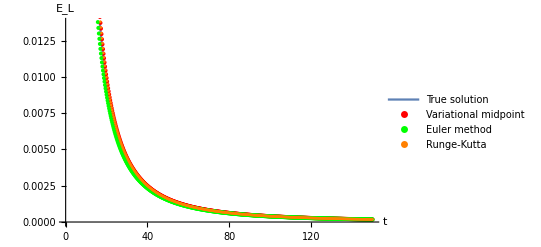

```mathematica
energy=Show[Plot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
ListPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","E_L"}]
```

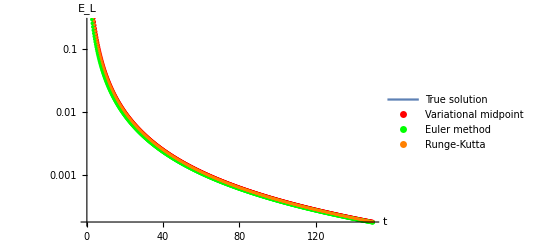

```mathematica
energylog=Show[LogPlot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListLogPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListLogPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
ListLogPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","E_L"}]
```